```mathematica
(* All teams AUDL 2017 stats *)
```

```mathematica
path=NotebookDirectory[]
```

C:\Users\User 1\Documents\Final-Project-Kacham\Ulti Analytics Summary Stats\

```mathematica
rawdata=Import["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\Ulti Analytics Summary Stats\\SummaryStatsAllTeams.xlsx","Data"]
```

{{{Year,Team,Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},821,{,,Total,,,,,,,,,,,,,,,,,,,,,,,,,}}}
 |  |  |  |

```mathematica
keys=rawdata[[1,1]]
```

{Year,Team,Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls}

```mathematica
Length[keys]
```

28

```mathematica
teamssummary2017= Dataset[Map[Association[Thread[Rule[keys,#]]]&,rawdata[[1,2;;Length[rawdata[[1]]]]]]]
```

Dataset[<>]

```mathematica
teamssummary2017set2 = teamssummary2017[All,{21->(Quantity[#,"Percent"]&)}][All,{24->(Quantity[#,"Percent"]&)}][All,{27 ->( Quantity[#,"Seconds"]&)}]
```

Dataset[<>]

```mathematica
totalPointsPlayedAllTeams = Total[teamssummary2017[All,If[!NumberQ[#["Points played"]],0,#["Points played"]]&]]
```

93293.5

```mathematica
totalOLine = Total[teamssummary2017[All,If[!NumberQ[#["O-line points played"]],0,#["O-line points played"]]&]]
```

46547.

```mathematica
totalDLine = Total[teamssummary2017[All,If[!NumberQ[#["D-line points played"]],0,#["D-line points played"]]&]]
```

46746.5

```mathematica
(* Comparing O-line points played to D-line points played *)
```

```mathematica
datasetcompare1 =teamssummary2017[All,{8,10}]
```

Dataset[<>]

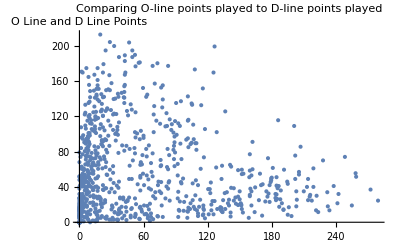

```mathematica
ListPlot[teamssummary2017[[All,{8,10}]],Axes->{True,True},Ticks->{None,Automatic},AxesLabel->{None,HoldForm["O Line and D Line Points"]},PlotLabel->"Comparing O-line points played to D-line points played"]
```

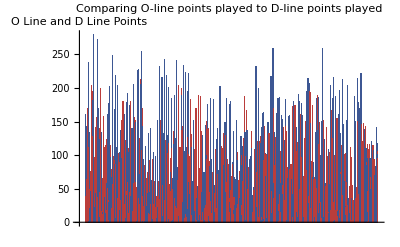

```mathematica
BarChart[datasetcompare1,ChartStyle->"DarkRainbow",Axes->{False,True},PlotLabel->"Comparing O-line points played to D-line points played",Ticks->{None,Automatic},AxesLabel->{None,HoldForm["O Line and D Line Points"]}]
```

```mathematica
(* Takeaway: there are more D-Line points played then O-line points *)
```

```mathematica
(* Comparing throwing percentages to catching percentages *)

datasetcompare2 = teamssummary2017set2[All, 21]
datasetcompare2set2 = teamssummary2017set2[All, 24]
```

Dataset[<>]

Dataset[<>]

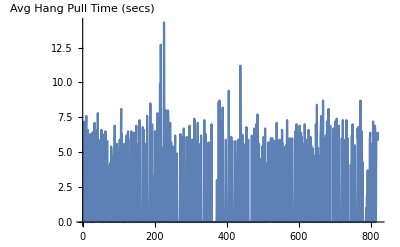

```mathematica
(* Compare team stats 2016 vs 2017 *)

(* Avg Pull Hang Time *)
(* Pulling is an underrated,incredibly important,and frequently difficult task for one of the seven players on every defensive line of a game.
If you're pulling for your team, you should be constantly reading both the wind and other team’s offense to try and learn what the best    type of pull is to get their offense to a slow or disrupted start. A good puller does 3 things well. They:
 Throw the disc far
	Throw the disc high
	Throw the disc accurately
Longer pull time- more time for defense to set up)
	A good pull is aimed diagonally 
  *)
(* This line plot shows the averege pull hang time that all players threw from the AUDL 2014-2017 season for multiple teams *)

ListLinePlot[teamssummary2017set2[All,27],AxesLabel->{None,HoldForm["Avg Hang Pull Time (secs)"]},Ticks->{None,Automatic}]
```

```mathematica
(* Seasonal Turnovers Trend (Turnovers per Touch)
(as the season progresses is the team experiencing more or less turns each game?) *)
```